```mathematica
pauliX[n_Integer]:=KroneckerProduct[IdentityMatrix[n/2],{{0,1},{1,0}}]

pauliY[n_Integer]:=KroneckerProduct[IdentityMatrix[n/2],{{0,-I},{I,0}}]

pauliZ[n_Integer]:=KroneckerProduct[IdentityMatrix[n/2],{{1,0},{0,-1}}]

Print[Dimensions[pauliX[8]]]
```

{8,8}

Clear kx

2 π

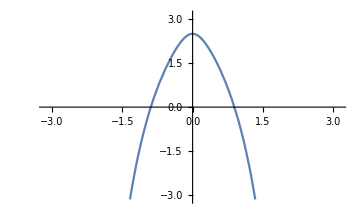

```mathematica
Clear kx
Clear[expr]
Clear[v]
T=2*Pi
H1[t_,kx_, beta_, alpha_] := Piecewise[{{(3*alpha/(4*T))*pauliX[2], 0 <= t <= T/3}, {(3*beta/(2*T))*(Cos[kx]*pauliX[2]-Sin[kx]*pauliY[2]), T/3 <= t <= 2*T/3}, {(3*alpha/(4*T))*pauliX[2], 2*T/3 <= t <= T}}]
U1[t_, kx_, beta_, alpha_] := Exp[-I*Integrate[H1[t1, kx, beta, alpha], {t1, 0, t}]]
Heff[kx_, epil_, beta_, alpha_] := If[epil==Pi,(I/T)*((2*Pi*I)+(Log[(U1[T/2, kx, beta, alpha])])/((Log[(epil)])+Pi*I)),(I/T)*(-(2*Pi*I)-(Log[-(U1[T/2, kx, beta, alpha])])/Log[(epil)])]
U1epil[t_, kx_, epil_, beta_, alpha_] := U1[t, kx, beta, alpha].(Exp[(I*t*Heff[kx, epil, beta, alpha])])
(*K = Tr[pauliZ[2]*Inverse[U1epil[T/2, kx, epil, beta, alpha]]*(D[U1epil[T/2,Pi, Pi, 1.8*Pi, 1.8*Pi]])]*)
(*Print[FullSimplify[K]]*)
kx=.; 

(**expr[kx_, beta_, alpha_]:=Tr[pauliZ[2]*Inverse[U1epil[T/2,kx,Pi,beta,alpha]]*(D[U1epil[T/2,kx,Pi,beta,alpha], kx])]; 
Manipulate[Plot[Re[expr[kx, beta, alpha]],{alpha, -2, 2}],{kx,-Pi,Pi},{beta, -2, 2}]*)
expr = Tr[pauliZ[2]*Inverse[U1epil[T/2,kx,Pi,1.8*Pi,1.9*Pi]]*(D[U1epil[T/2,kx,Pi,1.8*Pi,1.8*Pi], kx])];
Canvas[Plot[Re[expr],{kx,-Pi,Pi}, PlotRange->{{-Pi, Pi},{-Pi,Pi }}]]

(*v[kx_, epil_, beta_, alpha_] := 2(I/(4*Pi))*Integrate[Tr[pauliZ[2]*Inverse[U1epil[T/2, kx, epil, beta, alpha]]*(D[U1epil[T/2, kx, epil, beta, alpha], kx])], {kx, 0, 1.4}]*)
(*Print[FullSimplify[U1epil[T/2, kx, Pi, 1.8*Pi,1.8*Pi]]]*)
(*Print[v[kx,Pi, 1.8*Pi, 1.8*Pi]]*)
```

```mathematica
v[kx_, epil_, beta_, alpha_] := 2(I/(4*Pi))*Integrate[Tr[pauliZ[2]*Inverse[U1epil[T/2, kx, epil, beta, alpha]]*(D[U1epil[T/2, kx, epil, beta, alpha], kx])], {kx, 0, 0.6}]
(*Print[FullSimplify[U1epil[T/2, kx, Pi, 1.8*Pi,1.8*Pi]]]*)
Print[v[kx,Pi, 1.8*Pi, 1.9*Pi]]
```

Refine::fas: Warning: one or more assumptions evaluated to False.

Integrate::idiv: Integral of (ⅇ^(-1.41372 Sin[kx]) ((«1») Cos[kx]+ⅇ^((0.+1.41372 ⅈ) Cos[kx]) ((-1.32162-0.303256 ⅈ) ((«1») «1»)^(1/2 «1»)+«1») Sin[kx]))/((-0.987688-0.156434 ⅈ)+(«19»+«1») «1» «1»+ⅇ^((0.+2.82743 ⅈ) Cos[kx]) ((-1.+2.46725×10^-16 ⅈ)+1. («1»)^(«1») Times[«2»]^Times[«2»])) does not converge on {0,π}.

Refine::fas: Warning: one or more assumptions evaluated to False.

General::stop: Further output of Refine::fas will be suppressed during this calculation.

Integrate::idiv: Integral of (ⅇ^(-1.41372 Sin[kx]) ((«1») Cos[kx]+ⅇ^((0.+1.41372 ⅈ) Cos[kx]) ((-1.32162-0.303256 ⅈ) ((«1») «1»)^(1/2 «1»)+«1») Sin[kx]))/((-0.987688-0.156434 ⅈ)+(«19»+«1») «1» «1»+ⅇ^((0.+2.82743 ⅈ) Cos[kx]) ((-1.+2.46725×10^-16 ⅈ)+1. («1»)^(«1») Times[«2»]^Times[«2»])) does not converge on {0,π}.

1/(2 π)ⅈ ∫_0^π ((ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx])) ((-1.-1.22465×10^-16 ⅈ)+ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))) ((0.00351251+0.00127988 ⅈ) ((0.-56.5487 ⅈ) Cos[kx]-56.5487 Sin[kx])-(0.+0.025 ⅈ) ((0.+56.5487 ⅈ) Cos[kx]-56.5487 Sin[kx])))/((1.+2.44929×10^-16 ⅈ)-(1.+0. ⅈ) ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))+1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π])))-(1.+2.44929×10^-16 ⅈ) ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx])-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))+ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))+1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx])-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx])))-(ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx])) ((-1.-1.22465×10^-16 ⅈ)+ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))) ((0.-0.025 ⅈ) ((0.-56.5487 ⅈ) Cos[kx]-56.5487 Sin[kx])+(0.00351251+0.00127988 ⅈ) ((0.+56.5487 ⅈ) Cos[kx]-56.5487 Sin[kx])))/((1.+2.44929×10^-16 ⅈ)-(1.+0. ⅈ) ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))+1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π])))-(1.+2.44929×10^-16 ⅈ) ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx])-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))+ⅇ^(1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))+1/2 (-2 ⅈ π-Log[ⅇ^((0.-0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))]/(ⅈ π+Log[π]))-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]-(0.+56.5487 ⅈ) Sin[kx])-(0.+0.025 ⅈ) (59.6903+56.5487 Cos[kx]+(0.+56.5487 ⅈ) Sin[kx]))))ⅆkx

```mathematica
(*kx=.; 
expr=Tr[pauliZ[2]*Inverse[U1epil[T/2,kx,Pi,1.8*Pi,1.8*Pi]]*(D[U1epil[T/2,kx,Pi,1.8*Pi,1.8*Pi], kx])]; 

data = Catenate@
   Cases[Plot[Re[expr],{kx,-Pi,Pi}], Line[data_] :> data, Pi];
Export["file.txt", data, "Table"];
ListPlot[Import["file.txt", "Table"]]*)
```

```mathematica
M1 = (Exp[-I*2*Pi*1.35/3])*{{2+Cos[kx], 1+Exp[I*kx]},{1+Exp[-I*kx], 2+Cos[kx]}};
M2= MatrixLog[ResourceFunction["DiagonalizeMatrix"][{{2 + Cos[kx], 1+Exp[I*kx]}, {1+Exp[-I*kx], 2 + Cos[kx]}}]]/(I*Pi + Log[Pi]);
Heff = -I*Pi*(-1+((2*Pi*1.35)/3*(I*Pi + Log[Pi]))-((1/(I*Pi + Log[Pi])*M2)));
M3 = Exp[-I*Pi*(-1+((2*Pi*1.35)/3*(I*Pi + Log[Pi]))-((1/(I*Pi + Log[Pi])*M2)))];
Product = M1.M3;
ProductInv = Inverse[M1.M3];
DiffProduct = D[M1.M3, kx];
FinalExp = Tr[pauliZ[2]*Inverse[M1.M3]*D[M1.M3, kx]];
P1 = Graphics[Plot[Im[FinalExp], {kx, -Pi, Pi}]];
P2 = Graphics[Plot[Re[FinalExp], {kx, -Pi, Pi}, PlotStyle->Red]];
Show[P1, P2]
```

```mathematica
Integrate[Im[Evaluate[Tr[pauliZ[2]*Inverse[M1.M3]*D[M1.M3, kx]]]], {kx, 0, 2.3}]
```

```mathematica
Integrate[Evaluate[Tr[pauliZ[2]*Inverse[M1.M3]*D[M1.M3, kx]]], {kx, 0, 2.3}]
```

```mathematica
Integrate[Tr[pauliZ[2]*Inverse[M1.M3]*D[M1.M3, kx]], {kx, 0, 2.3}]
```

```mathematica
FullSimplify[%16]
```